```mathematica
f[x_,σ_]:=1/(√(2π)σ*x)*Exp[-((Log[x]+σ^2/2)^2)/(2*σ^2)]
```

```mathematica
Integrate[f[x,σ],{x,0,∞}]
```

√(1/σ^2) σ

```mathematica
Integrate[f[x,σ],{x,ω,∞}]
```

ConditionalExpression[(1/(√(1/σ^2))-σ Erf[(σ^2+2 Log[ω])/(2 √2 σ)])/(2 σ), Re[σ^2]≥0&&((Im[ω]==0&&Re[ω]>0)||ω∉ℝ)]

```mathematica
Integrate[f[x,σ],{x,0,ω}]
```

ConditionalExpression[(1/(√(1/σ^2))+σ Erf[(σ^2+2 Log[ω])/(2 √2 σ)])/(2 σ), Re[σ^2]>0]

```mathematica
Integrate[x*f[x,σ],{x,0,ω}]
```

ConditionalExpression[(1/(√(1/σ^2))-σ Erf[(σ^2-2 Log[ω])/(2 √2 σ)])/(2 σ), Re[σ^2]≥0]

```mathematica
Integrate[x*f[x,σ],{x,ω,∞}]
```

ConditionalExpression[(1/(√(1/σ^2))+σ Erf[(σ^2-2 Log[ω])/(2 √2 σ)])/(2 σ), Re[σ^2]>0&&((Im[ω]==0&&Re[ω]>0)||ω∉ℝ)]

```mathematica
Integrate[x*f[x,σ],{x,0,∞}]
```

√(1/σ^2) σ

```mathematica
Integrate[x*f[x,σ],{x,a,b}]
```

ConditionalExpression[1/2 (Erf[(σ^2-2 Log[a])/(2 √2 σ)]-Erf[(σ^2-2 Log[b])/(2 √2 σ)]), ]

```mathematica
σ[sigma_]:=Sqrt[Log[1+sigma^2]]
```

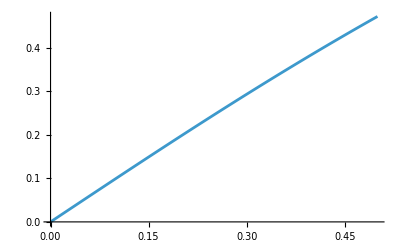

```mathematica
Plot[σ[s],{s,0,0.5}]
```

```mathematica
F[ω_,σ_]:=1/2(1-Erf[(Log[ω]+σ^2/2)/(σ*Sqrt[2])])
```

```mathematica
D[F[ω,σ],ω]
```

-(ⅇ^(-((σ^2/2+Log[ω])^2)/(2 σ^2)))/(√(2 π) σ ω)

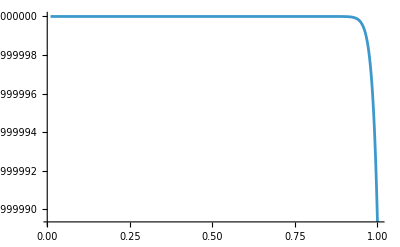

```mathematica
Plot[F[s*Exp[-(0.03-0.02)*30],0.07],{s,0.01,1},PlotRange->Full]
```

```mathematica
Fc[ω_,σ_]:=1/2(1+Erf[(Log[ω]-σ^2/2)/(σ*Sqrt[2])])
```

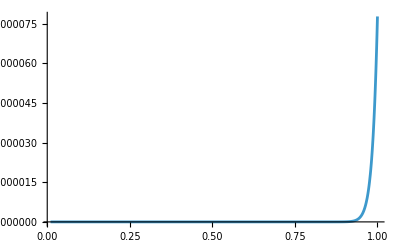

```mathematica
Plot[Fc[s*Exp[-(0.03-0.02)*30],0.07],{s,0.01,1},PlotRange->Full]
```

```mathematica
rhs1[s_,I_,d_,T_,σ_]:=s*Exp[d*T]*1/2(1+Erf[((I-d)*T-Log[s]-σ^2/2)/(σ*Sqrt[2])])
```

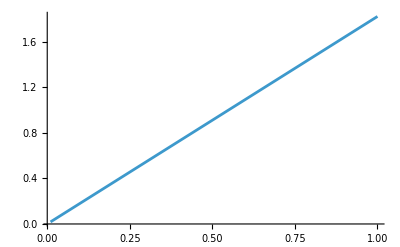

```mathematica
Plot[rhs1[s,0.03,0.02,30,0.07],{s,0.01,1},PlotRange->Full]
```

```mathematica
rhs2[s_,I_,d_,T_,σ_]:=Exp[I*T]*1/2(1-Erf[((I-d)*T-Log[s]+σ^2/2)/(σ*Sqrt[2])])
```

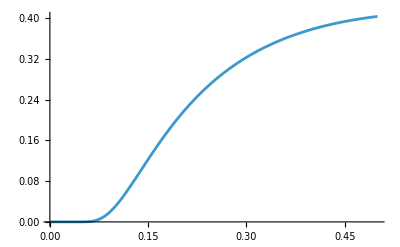

```mathematica
Plot[rhs2[0.95,0.015,0.01,30,σ],{σ,0.001,0.5},PlotRange->Full]
```

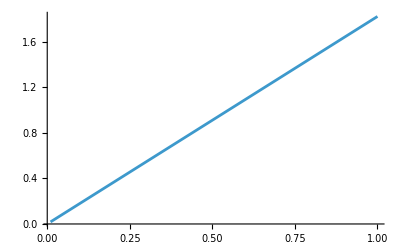

```mathematica
Plot[rhs1[s,0.03,0.02,30,0.07]+rhs2[s,0.03,0.02,30,0.07],{s,0.01,1},PlotRange->Full]
```

```mathematica
lhs[s_,f_,T_]:=s*Exp[f*T]
```

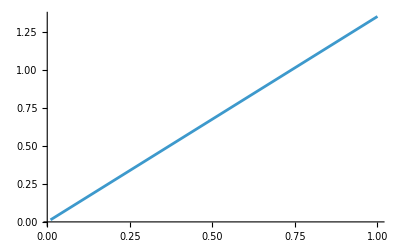

```mathematica
Plot[lhs[s,0.01,30],{s,0.01,1}]
```

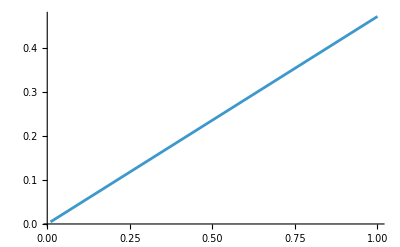

```mathematica
Plot[rhs1[s,0.03,0.02,30,0.07]+rhs2[s,0.03,0.02,30,0.07]-lhs[s,0.01,30],{s,0.01,1},PlotRange->Full]
```

```mathematica
splot[d_,I_,f_,T_,σ_]:=Plot[rhs1[s,I,d,T,σ]+rhs2[s,I,d,T,σ]-lhs[s,f,T],{s,0.01,1.2},PlotRange->Full]
```

```mathematica
dplot[s_,I_,f_,T_,σ_]:=Plot[rhs1[s,I,d,T,σ]+rhs2[s,I,d,T,σ]-lhs[s,f,T],{d,0.001,0.1},PlotRange->Full]
```

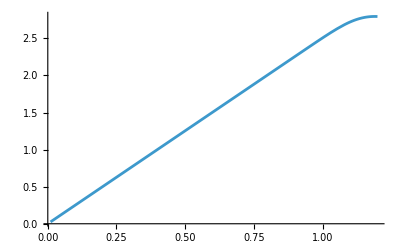

```mathematica
splot[0.045,0.05,0.01,30,0.07]
```

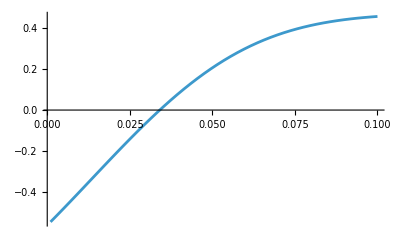

```mathematica
dplot[1.0,0.02,0.01,30,1.0]
```

```mathematica
rd[s_,I_,f_,T_,σ_]:=d/.FindRoot[0==-lhs[s,f,T]+rhs1[s,I,d,T,σ]+rhs2[s,I,d,T,σ],{d,0.015}]
```

```mathematica
rd[0.2,0.03,0.01,30,0.07]
```

0.01

```mathematica
rd[.8,0.02,0.01,30,0.9]
```

0.0214003

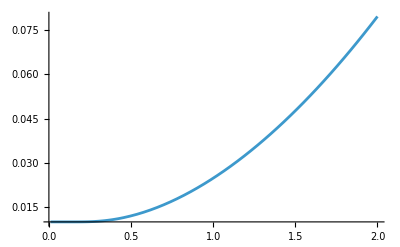

```mathematica
Plot[rd[0.8,0.02,0.01,30,σ],{σ,0.01,2.0}]
```

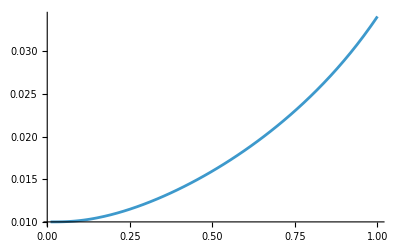

```mathematica
Plot[rd[s,0.02,0.01,30,1],{s,0.01,1.0}]
```

```mathematica
ωdef[s_,I_,d_,T_]:=s*Exp[(d-I)*T]
```

```mathematica
Fe[ω_,σ_]:=1/2(1+Erf[(-Log[ω]+σ^2/2)/(σ*Sqrt[2])])
```

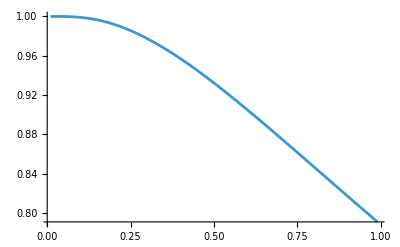

```mathematica
Plot[Fe[ωdef[s,0.03,0.02,30],1.0],{s,0.01,0.99}]
```

```mathematica
Fec[ω_,σ_]:=1/2(1+Erf[(-Log[ω]-σ^2/2)/(σ*Sqrt[2])])
```

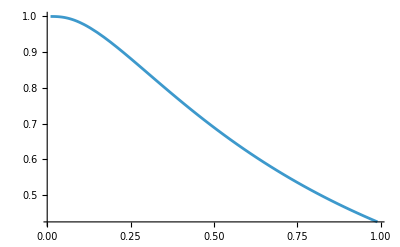

```mathematica
Plot[Fec[ωdef[s,0.03,0.02,30],1.0],{s,0.01,0.99}]
```

```mathematica
ExpET[s_,I_,d_,T_,σ_]:=Exp[I*T]/(1-s)*Fe[ωdef[s,I,d,T],σ]-(s*Exp[d*T])/(1-s)*Fec[ωdef[s,I,d,T],σ]
```

```mathematica
e[s_,I_,d_,T_,σ_]:=Log[ExpET[s,I,d,T,σ]]/T
```

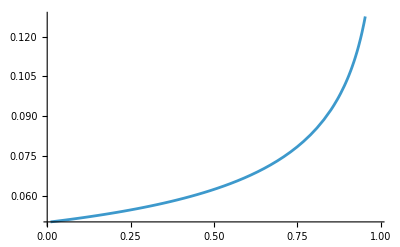

```mathematica
Plot[e[s,0.05,0.03,30,0.3],{s,0.01,0.99}]
```

```mathematica
rd[s_,I_,f_,T_,σ_]:=d/. FindRoot[0==-lhs[s,f,T]+rhs1[s,I,d,T,σ]+rhs2[s,I,d,T,σ],{d,0.015,0.,0.999},AccuracyGoal->8,PrecisionGoal->8,MaxIterations->1000 (*Guess,Min,Max*)]
```

```mathematica
enum[s_,I_,f_,T_,σ_]:=Log[ExpET[s,I,rd[s,I,f,T,σ],T,σ]]/T
```

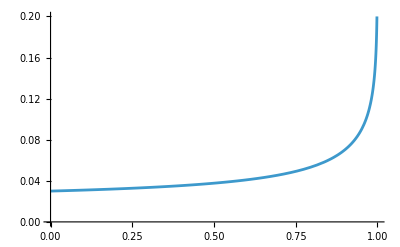

```mathematica
Plot[enum[s,0.03,0.02,30,0.3],{s,0.,0.99999},PlotRange->{0,0.2}]
```

```mathematica
OneMinusSExpET[s_,I_,d_,T_,σ_]:=Exp[I*T]*Fe[ωdef[s,I,d,T],σ]-s*Exp[d*T]*Fec[ωdef[s,I,d,T],σ]
```

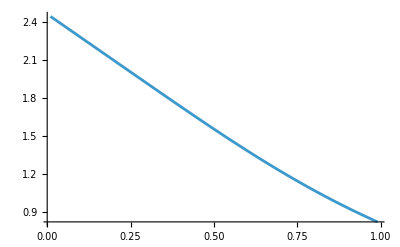

```mathematica
Plot[OneMinusSExpET[s,0.03,0.02,30,0.5],{s,0.01,0.99}]
```

```mathematica
OneMinusSExpETnum[s_,I_,f_,T_,σ_]:=OneMinusSExpET[s,I,rd[s,I,f,T,σ],T,σ]
```

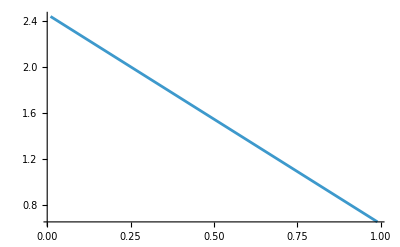

```mathematica
Plot[OneMinusSExpETnum[s,0.03,0.02,30,0.5],{s,0.01,0.99}]
```